## Plotting functions given output of GeomComp_Compute.nb

## Preliminaries

```mathematica
Clear["Global`*"]
SetDirectory[FileNameJoin[{NotebookDirectory[],"results/"}]] 
Get["GeomCompP1var.txt"];
Get["GeomCompP1fix.txt"];
Get["GeomCompP2var.txt"];
Get["GeomCompP2fix.txt"];
Get["GeomCompP3var.txt"];
Get["GeomCompP3fix.txt"];
SetDirectory[FileNameJoin[{NotebookDirectory[],"../figs/"}]]
```

/Users/marknovak/Git/aaaManuscripts/GeometricComplexity/mathematica/results

/Users/marknovak/Git/aaaManuscripts/GeometricComplexity/figs

### Functions to compute and append relative (ratios of) complexity values

denom_ is the measure to which the list of all numer_ measures are compared

```mathematica
Relativize[data_,denom_,numer_]:=
Transpose[
Table[
data[[All,i]]/data[[All,denom]],
{i,numer}
]];
AppendRelativized[data_,denom_,numer_]:=
Join[data,Relativize[data,denom,numer],2];
```

```mathematica
AppendRelativized[GeomCompP1fix,3,{4}]
```

{{5,2,3.55047,3.44537,0.970396},{5,3,3.53827,3.44537,0.973744},{5,4,3.53681,3.44537,0.974146},{5,5,3.53339,3.44537,0.975087},{6,2,3.5501,3.44334,0.969929},{6,3,3.53787,3.44334,0.973281},{6,4,3.52912,3.44334,0.975693},{6,5,3.52763,3.44334,0.976105},{7,2,3.54765,3.44165,0.970122},{7,3,3.53508,3.44165,0.973571},{7,4,3.52669,3.44165,0.975886},{7,5,3.525,3.44165,0.976356},{8,2,3.5459,3.43931,0.969941},{8,3,3.53105,3.43931,0.974017},{8,4,3.52503,3.43931,0.975682},{8,5,3.52064,3.43931,0.976899},{9,2,3.54548,3.439,0.969968},{9,3,3.53112,3.439,0.973913},{9,4,3.52506,3.439,0.975586},{9,5,3.52102,3.439,0.976706}}

### Define generic plotting function

```mathematica
MyListLinePlot[
data_,
axislabels_,
plotlabel_,
plotRange_]:=
ListLinePlot[Apply[{#1,#3}&,
SortBy[Cases[Normal@
ListPlot3D[
data,
PlotRange->All,
InterpolationOrder->1,
Mesh-> {{0},DeleteDuplicates[data[[All,2]]]},
ScalingFunctions->{"Linear","Linear","Linear"},
BoundaryStyle->None,
Boxed->False,
Axes->False],
Line[a_]:>a,Infinity],{2}],
{2}],
ScalingFunctions->{"Log","Log"}, 
PlotStyle->ColorData[49,"ColorList"],
GridLines->{None,{1}},
GridLinesStyle->Directive[LightGray, Dashed],
PlotRange->plotRange,
Frame-> True,
FrameLabel-> axislabels,
PlotLabel->plotlabel]
```

```mathematica
data=AppendRelativized[GeomCompP1fix,3,{4}]
```

{{5,2,3.55047,3.44537,0.970396},{5,3,3.53827,3.44537,0.973744},{5,4,3.53681,3.44537,0.974146},{5,5,3.53339,3.44537,0.975087},{6,2,3.5501,3.44334,0.969929},{6,3,3.53787,3.44334,0.973281},{6,4,3.52912,3.44334,0.975693},{6,5,3.52763,3.44334,0.976105},{7,2,3.54765,3.44165,0.970122},{7,3,3.53508,3.44165,0.973571},{7,4,3.52669,3.44165,0.975886},{7,5,3.525,3.44165,0.976356},{8,2,3.5459,3.43931,0.969941},{8,3,3.53105,3.43931,0.974017},{8,4,3.52503,3.43931,0.975682},{8,5,3.52064,3.43931,0.976899},{9,2,3.54548,3.439,0.969968},{9,3,3.53112,3.439,0.973913},{9,4,3.52506,3.439,0.975586},{9,5,3.52102,3.439,0.976706}}

## Plot ratio of Geometric complexities - varying max abundance levels

```mathematica
axislabelsLineComp={"Max. prey abundance","Flexibility"};
axislabelsLineRel={"Max. prey abundance","Relative flexibility"};
```

```mathematica
data=GeomCompP1var[[All,{1,2,3}]];
p1varH1=MyListLinePlot[data,
axislabelsLineComp,
"Holling Type I",
{All,All}
];

data=AppendRelativized[GeomCompP1fix,3,{4}];
p1varH1vR=MyListLinePlot[
data,
axislabelsLineRel,
"Ratio / Holling Type I",
{All,{All,1}}
];
```

```mathematica
data=GeomCompP2var[[All,{1,2,3}]];
p2varH2=MyListLinePlot[data,
axislabelsLineComp,
"Holling Type II",
{All,{3,8.5}}
];

data=GeomCompP2var[[All,{1,2,6}]];
p2varH2vHV=MyListLinePlot[
data,
axislabelsLineRel,
"Hassell-Varley / Holling Type II",
{All,{0.98,All}}
];

data=GeomCompP2var[[All,{1,2,7}]];
p2varH2vAG=MyListLinePlot[
data,
axislabelsLineRel,
"Arditi-Ginzburg / Holling Type II",
{All,{0.98,All}}
];
```

```mathematica
data=GeomCompP3var[[All,{1,2,3}]];
p3varBD=MyListLinePlot[data,
axislabelsLineComp,
"Beddington-DeAngelis",
{All,All}
];

data=GeomCompP3var[[All,{1,2,6}]];
p3varBDvCM=MyListLinePlot[
data,
axislabelsLineRel,
"Crowley-Martin / Beddington-DeAngelis",
{All,{0.98,All}}
];

data=GeomCompP3var[[All,{1,2,7}]];
p3varBDvAA=MyListLinePlot[
data,
axislabelsLineRel,
"Arditi-Akcakaya / Beddington-DeAngelis",
{All,{0.98,All}}
];
```

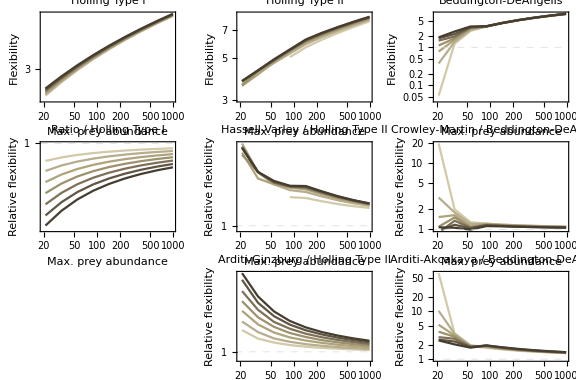

GeomComp_var_line.pdf

```mathematica
AllVar=
Legended[
GraphicsGrid[{
{p1varH1,p2varH2,p3varBD},
{p1varH1vR,p2varH2vHV,p3varBDvCM},
{"",p2varH2vAG,p3varBDvAA}},
ImageSize-> Large],
Placed[
LineLegend[
ColorData[49,"ColorList"],
DeleteDuplicates[data[[All,2]]],
LegendLabel->"Max. predator abundance",
LegendLayout->"Row"],
Above]]

Export["GeomComp_var_line.pdf",AllVar]
```

## Plot ratio of Geometric complexities - fixed max abundance levels

```mathematica
axislabelsLineComp={"Prey levels","Flexibility"};
axislabelsLineRel={"Prey levels","Relative flexibility"};
```

```mathematica
data=GeomCompP1fix[[All,{1,2,3}]];
p1fixH1=MyListLinePlot[data,
axislabelsLineComp,
"Holling Type I",
{All,All}
];

data=GeomCompP1fix[[All,{1,2,5}]];
p1fixH1vR=MyListLinePlot[
data,
axislabelsLineRel,
"Ratio / Holling Type I",
{All,{All,1.001}}
];
```

```mathematica
data=GeomCompP2fix[[All,{1,2,3}]];
p2fixH2=MyListLinePlot[data,
axislabelsLineComp,
"Holling Type II",
{All,All}
];

data=GeomCompP2fix[[All,{1,2,6}]];
p2fixH2vHV=MyListLinePlot[
data,
axislabelsLineRel,
"Hassell-Varley / Holling Type II",
{All,{0.99,All}}
];

data=GeomCompP2fix[[All,{1,2,7}]];
p2fixH2vAG=MyListLinePlot[
data,
axislabelsLineRel,
"Arditi-Ginzburg / Holling Type II",
{All,{0.99,All}}
];
```

```mathematica
data=GeomCompP3fix[[All,{1,2,3}]];
p3fixBD=MyListLinePlot[data,
axislabelsLineComp,
"Beddington-DeAngelis",
{All,All}
];

data=GeomCompP3fix[[All,{1,2,6}]];
p3fixBDvCM=MyListLinePlot[
data,
axislabelsLineRel,
"Crowley-Martin / Beddington-DeAngelis",
{All,{0.98,All}}
];

data=GeomCompP3fix[[All,{1,2,7}]];
p3fixBDvAA=MyListLinePlot[
data,
axislabelsLineRel,
"Arditi-Akcakaya / Beddington-DeAngelis",
{All,{0.98,All}}
];
```

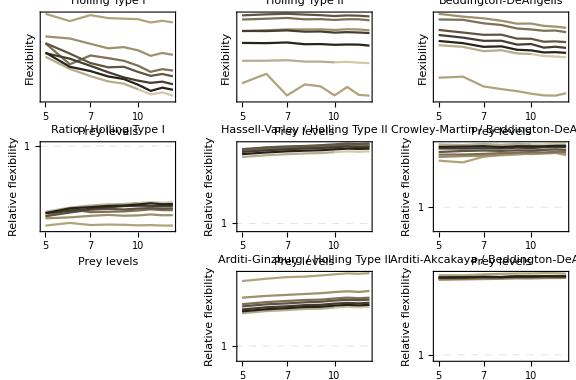

GeomComp_fix_line.pdf

```mathematica
AllFix=
Legended[
GraphicsGrid[{
{p1fixH1,p2fixH2,p3fixBD},
{p1fixH1vR,p2fixH2vHV,p3fixBDvCM},
{"",p2fixH2vAG,p3fixBDvAA}},
ImageSize-> Large],
Placed[
LineLegend[
ColorData[49,"ColorList"],
DeleteDuplicates[data[[All,2]]],
LegendLabel->"Predator levels",
LegendLayout->"Row"],
Above]]

Export["GeomComp_fix_line.pdf",AllFix]
```